# octet.experiment.data.nb

```mathematica
NotebookFileName[]
```

C:\Users\Tom\Desktop\octet.experiment.data.nb

this nb is to record the octet ge gm experiment data.

## initial

```mathematica
Needs["ErrorBarPlots`"]
```

## nucleon`ge`total

```mathematica
data`nucleon`ge`total={{{0.00955928,0.00284004},ErrorBar[0.00219944]},{{0.0391061,0.0202351},ErrorBar[0.0141688]},{{0.0877716,0.0427733},ErrorBar[0.0236317]},{{0.149845,0.0481009},ErrorBar[0.0116624]},{{0.209683,0.0660114},ErrorBar[0.0189258]},{{0.255369,0.0659661},ErrorBar[0.0450128]},{{0.300559,0.0552302},ErrorBar[0.00787724]},{{0.339789,0.0679462},ErrorBar[0.0128389]},{{0.475605,0.0528741},ErrorBar[0.00905371]},{{0.58982,0.047748},ErrorBar[0.00890026]},{{0.670267,0.0468631},ErrorBar[0.00905366]},{{0.789944,0.0468529},ErrorBar[0.0114578]},{{1.,0.0454987},ErrorBar[0.00531969]},{{1.13234,0.0395565},ErrorBar[0.00404087]},{{1.1743,0.0438074},ErrorBar[0.00946292]},{{1.39702,0.0326083},ErrorBar[0.0113555]},{{1.4504,0.0413107},ErrorBar[0.00470588]}};
```

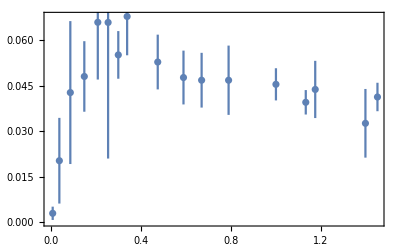

```mathematica
fig`nucleon`ge`total=ErrorListPlot[
data`nucleon`ge`total,
(*figure configurations*)
AxesOrigin->{0,0},
PlotRange->{Full,Full},
PlotRangePadding->{Automatic,Scaled[.3]},
ImageSize->Scaled[0.4],
AspectRatio->1/GoldenRatio,
Frame->True
]
```

## total

-Graphics-Nucleon.Ge.total

## nucleon`ge`light-sea

## original

{{{0,-5.11533*10^-6},ErrorBar[0.000121212]},{{0.0500921,0.00251469},ErrorBar[0.00100699]},{{0.100184,0.00380839},ErrorBar[0.00126805]},{{0.149982,0.00439815},ErrorBar[0.0015198]},{{0.200074,0.00449838},ErrorBar[0.00193008]},{{0.250166,0.00474779},ErrorBar[0.00211655]},{{0.30011,0.00491796},ErrorBar[0.00223776]},{{0.350055,0.00455199},ErrorBar[0.00257343]},{{0.399853,0.00462892},ErrorBar[0.00316085]},{{0.449797,0.00522333},ErrorBar[0.00357111]},{{0.49989,0.00455433},ErrorBar[0.00410256]}}

```mathematica
data`nucleon`ge`lightsea={
{{0,(3)*0},ErrorBar[0]},
{{0.05,(3)*0.00251469},ErrorBar[(3)*0.00100699]},
{{0.1,(3)*0.00380839},ErrorBar[(3)*0.00126805]},
{{0.15,(3)*0.00439815},ErrorBar[(3)*0.0015198]},
{{0.2,(3)*0.00449838},ErrorBar[(3)*0.00193008]},
{{0.25,(3)*0.00474779},ErrorBar[(3)*0.00211655]},
{{0.3,(3)*0.00491796},ErrorBar[(3)*0.00223776]},
{{0.35,(3)*0.00455199},ErrorBar[(3)*0.00257343]},
{{0.4,(3)*0.00462892},ErrorBar[(3)*0.00316085]},
{{0.45,(3)*0.00522333},ErrorBar[(3)*0.00357111]},
{{0.5,(3)*0.00455433},ErrorBar[(3)*0.00410256]}
};
```

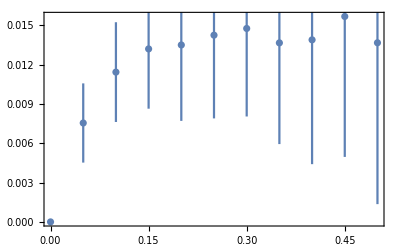

```mathematica
fig`exp`nucleon`ge`lightsea=ErrorListPlot[
data`nucleon`ge`lightsea,
(*figure configurations*)
AxesOrigin->{0,0},
PlotRange->{All,All},
PlotRangePadding->{Automatic,Automatic},
ImageSize->Scaled[0.5],
AspectRatio->1/GoldenRatio,
Frame->True
]
```

## nucleon`ge`strange

```mathematica
data`nucleon`ge`s={
{{0,0},ErrorBar[0]},
{{0.05,0.001124702644},ErrorBar[0.00042369]},
{{0.1,0.001707193768},ErrorBar[0.000616653]},
{{0.15,0.002246189851},ErrorBar[0.000778041]},
{{0.2,0.002231676992},ErrorBar[0.000833645]},
{{0.25,0.002445556207},ErrorBar[0.000945724]},
{{0.3,0.002659845718},ErrorBar[0.00104725]},
{{0.35,0.002726435358},ErrorBar[0.00112127]},
{{0.4,0.002756239279},ErrorBar[0.00114272]},
{{0.45,0.003696516179},ErrorBar[0.00132153]},
{{0.5,0.003632884057},ErrorBar[0.00138048]}};
```

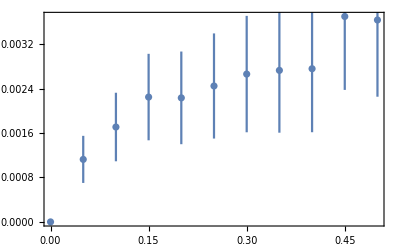

```mathematica
fig`exp`nucleon`ge`s=ErrorListPlot[
data`nucleon`ge`s,
(*figure configurations*)
AxesOrigin->{0,0},
PlotRange->{Full,Full},
PlotRangePadding->{Automatic,Scaled[.3]},
ImageSize->Scaled[0.4],
AspectRatio->1/GoldenRatio,
Frame->True
]
```

## nucleon`gm`lightsea

## origin

{
{{-0.00014477,(3)*-0.0433074},ErrorBar[(3)*0.0120623]},
{{0.0499457,(3)*-0.0394942},ErrorBar[(3)*0.0145525]},
{{0.0998914,(3)*-0.0366926},ErrorBar[(3)*0.00972763]},
{{0.149982,(3)*-0.0353307},ErrorBar[(3)*0.00824903]},
{{0.200072,(3)*-0.0335798},ErrorBar[(3)*0.00785992]},
{{0.250018,(3)*-0.0268872},ErrorBar[(3)*0.00723735]},
{{0.299964,(3)*-0.0244358},ErrorBar[(3)*0.00653696]},
{{0.350199,(3)*-0.0232296},ErrorBar[(3)*0.00599222]},
{{0.400145,(3)*-0.0201556},ErrorBar[(3)*0.00638132]},
{{0.450235,(3)*-0.0124514},ErrorBar[(3)*0.00513619]},
{{0.500036,(3)*-0.00451362},ErrorBar[(3)*0.00342412]}
};

```mathematica
data`nucleon`gm`lightsea={
{{0,(3)*-0.0433074},ErrorBar[(3)*0.0120623]},
{{0.05,(3)*-0.0394942},ErrorBar[(3)*0.0145525]},
{{0.10,(3)*-0.0366926},ErrorBar[(3)*0.00972763]},
{{0.15,(3)*-0.0353307},ErrorBar[(3)*0.00824903]},
{{0.20,(3)*-0.0335798},ErrorBar[(3)*0.00785992]},
{{0.25,(3)*-0.0268872},ErrorBar[(3)*0.00723735]},
{{0.30,(3)*-0.0244358},ErrorBar[(3)*0.00653696]},
{{0.35,(3)*-0.0232296},ErrorBar[(3)*0.00599222]},
{{0.40,(3)*-0.0201556},ErrorBar[(3)*0.00638132]},
{{0.45,(3)*-0.0124514},ErrorBar[(3)*0.00513619]},
{{0.50,(3)*-0.00451362},ErrorBar[(3)*0.00342412]}
};
```

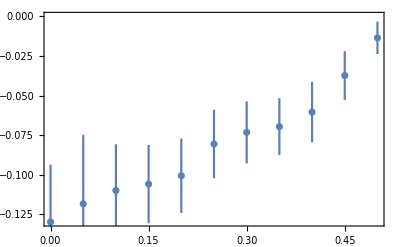

```mathematica
fig`exp`nucleon`gm`lightsea=ErrorListPlot[
data`nucleon`gm`lightsea,
(*figure configurations*)
AxesOrigin->{0,0},
PlotRange->{Full,Full},
PlotRangePadding->{Automatic,Scaled[.3]},
ImageSize->Scaled[0.4],
AspectRatio->1/GoldenRatio,
Frame->True
]
```

## nucleon`gm`strange

```mathematica
data`nucleon`gm`s={
{{0,-0.06423700498},ErrorBar[0.0168356]},
{{0.05,-0.04284891793},ErrorBar[0.0102095]},
{{0.1,-0.03743683104},ErrorBar[0.0114205]},
{{0.15,-0.02424724195},ErrorBar[0.00621208]},
{{0.2,-0.01849545279},ErrorBar[0.00479972]},
{{0.25,-0.01771258857},ErrorBar[0.00435548]},
{{0.3,-0.01543411254},ErrorBar[0.00428035]},
{{0.35,-0.01239120693},ErrorBar[0.00505773]},
{{0.4,-0.0107490449},ErrorBar[0.00535843]},
{{0.45,-0.01032118392},ErrorBar[0.00614265]},
{{0.5,-0.007114672445},ErrorBar[0.00564711]}
};
```

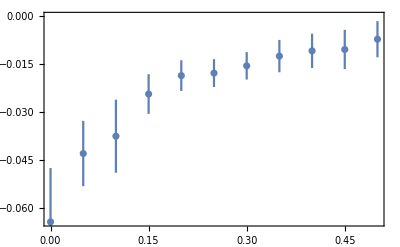

```mathematica
fig`exp`nucleon`gm`s=ErrorListPlot[
data`nucleon`gm`s,
(*figure configurations*)
AxesOrigin->{0,0},
PlotRange->{Full,Full},
PlotRangePadding->{Automatic,Scaled[.3]},
ImageSize->Scaled[0.4],
AspectRatio->1/GoldenRatio,
Frame->True
]
```